```mathematica
exp=Sum[ (ⅈ θ)^j/(j!),{j, 0, 5}]
```

1+ⅈ θ-θ^2/2-(ⅈ θ^3)/6+θ^4/24+(ⅈ θ^5)/120

```mathematica
Series[E^x,{x,0, 7}]
Series[Sin[x],{x,0, 7}]
Series[Cos[x],{x,0, 7}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+O[x]^8

x-x^3/6+x^5/120-x^7/5040+O[x]^8

1-x^2/2+x^4/24-x^6/720+O[x]^8

```mathematica
Integrate[E^x Cos[x],x]
```

1/2 ⅇ^x (Cos[x]+Sin[x])

Re[∫E^x E^(ⅈ x)]=Re[∫E^((ⅈ+1) x)] = Re[E^((ⅈ+1) x)/(1+ⅈ)]

```mathematica
Simplify[Exp[ⅈ θ]-(Cos[θ]+ⅈ Sin[θ])]
```

0

# Project 13 DFT

Available data.

```mathematica
ExampleData["Audio"]
Talk=ExampleData[{"Audio","Apollo11ReturnSafely"}]
```

{{Audio,Apollo11ReturnSafely},{Audio,Apollo11SmallStep},{Audio,BalloonPop},{Audio,Bee},{Audio,Bird},{Audio,BlackcapWarbler},{Audio,Cat},{Audio,Cello},{Audio,CelloScale},{Audio,ChurchBell},{Audio,Clapping},{Audio,CreakyDoor},{Audio,Crowd},{Audio,DogBark},{Audio,Drums},{Audio,FemaleVoice},{Audio,Flute},{Audio,FluteScale},{Audio,FogHorn},{Audio,IRMaesHowe},{Audio,IRRailwayTunnel},{Audio,IRSportsCenter},{Audio,IRStairway},{Audio,IRStAndrewsChurch},{Audio,IRStMarysChurch},{Audio,IRYorkMinsterChurch},{Audio,Laughing},{Audio,MaleVoice},{Audio,NoisyTalk},{Audio,Piano},{Audio,PianoScale},{Audio,PowerSupply},{Audio,Scream},{Audio,SubwayTrain},{Audio,Sword},{Audio,ThaiBells},{Audio,Walking},{Audio,Water},{Audio,Wind}}

```mathematica
ExampleData["Sound"]
ExampleData[{"Sound","TubaScale"}]
```

{{Sound,AltoFlute},{Sound,AltoFluteScale},{Sound,AltoSaxophone},{Sound,AltoSaxophoneScale},{Sound,Apollo11PhoneCall},{Sound,Apollo11ReturnSafely},{Sound,Apollo11SmallStep},{Sound,Apollo13Countdown},{Sound,Apollo13Problem},{Sound,BalloonPop},{Sound,BassClarinet},{Sound,BassClarinetScale},{Sound,BassFlute},{Sound,BassFluteScale},{Sound,Bassoon},{Sound,BassoonScale},{Sound,BassTrombone},{Sound,BassTromboneScale},{Sound,BlackcapWarbler},{Sound,Burst100},{Sound,Burst1000},{Sound,Burst7350},{Sound,Cello},{Sound,CelloPizzicato},{Sound,CelloPizzicatoScale},{Sound,CelloScale},{Sound,Clarinet},{Sound,ClarinetScale},{Sound,CrashCymbal},{Sound,DoubleBass},{Sound,DoubleBassPizzicato},{Sound,DoubleBassPizzicatoScale},{Sound,DoubleBassScale},{Sound,Flute},{Sound,FluteScale},{Sound,FrenchHorn},{Sound,FrenchHornScale},{Sound,JetSound},{Sound,LinearSweep},{Sound,NoiseBlue},{Sound,NoiseBrown},{Sound,NoisePink},{Sound,NoiseViolet},{Sound,NoiseWhite},{Sound,Oboe},{Sound,OboeScale},{Sound,OrganChord},{Sound,Piano},{Sound,PianoScale},{Sound,RollingCoin},{Sound,SopranoSaxophone},{Sound,SopranoSaxophoneScale},{Sound,Square10},{Sound,Square100},{Sound,Square1000},{Sound,Square7350},{Sound,SubwayTrain},{Sound,TenorTrombone},{Sound,TenorTromboneScale},{Sound,TestIntermodulationDistortion},{Sound,Trumpet},{Sound,TrumpetScale},{Sound,Tuba},{Sound,TubaScale},{Sound,Viola},{Sound,ViolaScale},{Sound,Violin},{Sound,ViolinScale}}

-Graphics-

```mathematica
Hmm=ExampleData["TestImage"]
ExampleData[{"TestImage","Moon"}]
```

{{TestImage,Aerial},{TestImage,Aerial2},{TestImage,Airplane},{TestImage,Airplane2},{TestImage,Airport},{TestImage,APC},{TestImage,Apples},{TestImage,Boat},{TestImage,Bridge},{TestImage,CarAndAPC},{TestImage,CarAndAPC2},{TestImage,ChemicalPlant},{TestImage,Clock},{TestImage,Couple},{TestImage,Couple2},{TestImage,Elaine},{TestImage,F16},{TestImage,Flower},{TestImage,Girl},{TestImage,Girl2},{TestImage,Girl3},{TestImage,Gray21},{TestImage,House},{TestImage,House2},{TestImage,JellyBeans},{TestImage,JellyBeans2},{TestImage,Lena},{TestImage,Man},{TestImage,Mandrill},{TestImage,Marruecos},{TestImage,Moon},{TestImage,Numbers},{TestImage,Peppers},{TestImage,RadcliffeCamera},{TestImage,ResolutionChart},{TestImage,Ruler},{TestImage,Sailboat},{TestImage,Splash},{TestImage,Stall},{TestImage,Tank},{TestImage,Tank2},{TestImage,Tank3},{TestImage,TestPattern},{TestImage,Tiffany},{TestImage,Tree},{TestImage,Truck},{TestImage,TruckAndAPC},{TestImage,TruckAndAPC2},{TestImage,U2},{TestImage,Volubilis}}

-Graphics-

```mathematica
Hmm=ExampleData["TestImage3D"]
ExampleData[Hmm⟦4⟧]
```

{{TestImage3D,CTengine},{TestImage3D,CThead},{TestImage3D,MRbrain},{TestImage3D,MRknee},{TestImage3D,Orbits}}

-Graphics3D-

```mathematica
ExampleData["TestImage3D"]
```

## 1D: Sound

#### Sampled Sound

```mathematica
Talk=ExampleData[{"Audio","NoisyTalk"}]
```

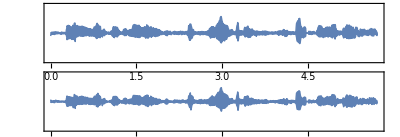

```mathematica
AudioPlot[Talk]
```

#### Synthesized Sound and DFTs

```mathematica
TabView[{
"220Hz"->Play[Sin[220 2Pi t],{t,0,1}],
"440Hz"->Play[Sin[440 2Pi t],{t,0,1}],
"880Hz"->Play[Sin[880 2Pi t],{t,0,1}]}]
```

123

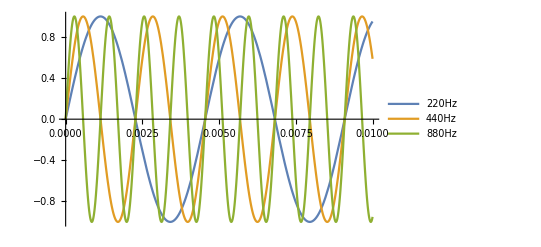

```mathematica
Plot[{Sin[220 2Pi t],Sin[440 2Pi t],Sin[880 2Pi t]},
{t,0,0.01},
PlotLegends->{"220Hz","440Hz","880Hz"}]
```

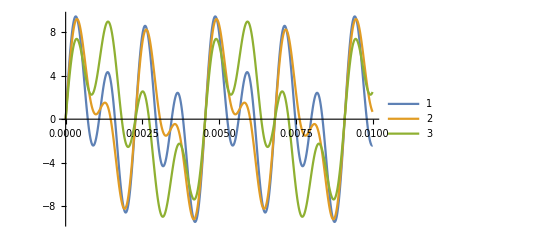

```mathematica
Plot[{
Sin[220 2Pi t]+4Sin[440 2Pi t]+6Sin[880 2Pi t],
Sin[220 2Pi t]+6Sin[440 2Pi t]+4Sin[880 2Pi t],
6Sin[220 2Pi t]+1Sin[440 2Pi t]+4Sin[880 2Pi t]},
{t,0,0.01},
PlotLegends->Automatic]
```

They a sound very similar. What you mainly hear is the fundamental “lowest” frequency in any sum of these three harmonic frequencies.

```mathematica
TabView[{
"1-4-6"->Play[Sin[220 2Pi t]+4Sin[440 2Pi t]+6Sin[880 2Pi t],{t,0,1}],
"1-6-4"->Play[Sin[220 2Pi t]+6Sin[440 2Pi t]+4Sin[880 2Pi t],{t,0,1}],
"6-1-4"->Play[6Sin[220 2Pi t]+1Sin[440 2Pi t]+4Sin[880 2Pi t],{t,0,1}]}]
```

123

The DFT lets you split out the frequencies.

```mathematica
SoundData= Table[ 1Sin[220 2Pi t]+6.0Sin[440 2Pi t]+4.0Sin[880 2Pi t],{t,0.0,1,1/8000 }];
FreqData=Fourier[SoundData];
TabView[{
"Big Picture"->ListPlot[Abs[FreqData],PlotRange->All,Joined->True],
"Small Picture"->ListPlot[Abs[FreqData]⟦1;;10^3⟧,PlotRange->All,Joined->True],
"Scaled-Small Picture"->ListPlot[(Abs[FreqData]⟦1;;10^3⟧)/Max[Abs[FreqData]],
PlotRange->All,Joined->True,
GridLines->{{220,440,880},{1,1/6,2/3}}]}
]
```

123

What happens if the sound is longer.

```mathematica
SoundData= Table[ 1Sin[220 2Pi t]+6.0Sin[440 2Pi t]+4.0Sin[880 2Pi t],{t,0.0,2,1/8000 }];
FreqData=Fourier[SoundData];
TabView[{
"Big Picture"->ListPlot[Abs[FreqData],PlotRange->All,Joined->True],
"Small Picture"->ListPlot[Abs[FreqData]⟦1;;10^3⟧,PlotRange->All,Joined->True],
"Scaled-Small Picture"->ListPlot[(Abs[FreqData]⟦1;;2*10^3⟧)/Max[Abs[FreqData]],
PlotRange->All,Joined->True,
GridLines->{{220,440,880},{1,1/6,2/3}}]}
]
```

123

In words, the DFT splits up a sound into ....

#### Sampled Sound

Back to our sampled sound

```mathematica
Talk=ExampleData[{"Audio","NoisyTalk"}]
{Track1,Track2}=AudioData[Talk];
ListPlot[{Track1,Track2},PlotRange->All]
```

12

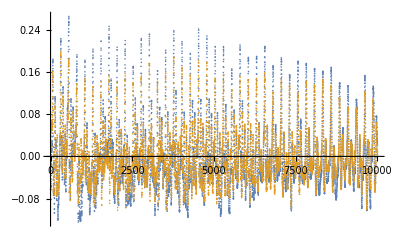

12

```mathematica
clip=2*10^4;;3*10^4;
ListPlot[{Track1⟦clip⟧,Track2⟦clip⟧},PlotRange->All]
FreqData=Fourier[Track1⟦clip⟧];
TabView[{
"Big Picture"->ListPlot[Abs[FreqData],PlotRange->All],
"Close Up"->ListPlot[Abs[FreqData]⟦1;;500⟧,PlotRange->All,GridLines->Automatic,Joined->True]
}]
```

To translate the wiggles in the window scale into frequency we need to know the length of the window and the number of data points per second in the original data.

#### The DFT again

The DFT is the linear transformation that splits a signal x_(0:n-1) of length n up into the components in each wiggle number k.  The recipe
	X_k=∑_(j=0)^(n-1) x_j ⅇ^(-(2π ⅈ)/nk j)
is explained by the first video.  In the language of the video is the center of mass of the data x_(0:n-1) wrapped around the unit circle k times.  Wrapped zero times looks a little special.  Electrical engineers call X_0 the DC component: it is just the sum of the entries of x.    Here is a small periodic data set.  Electrical Engineers, Physicists, and Mathematicians use different scalings.   The optional argument in Fourier uses the “data-analysis” standard. Note that the definition is zero based while most people and software tools do linear algebra with the lowest entry in slot one.

256

{7.2,1.7,0,3.15-0.5 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.15+0.5 ⅈ,0,1.7}

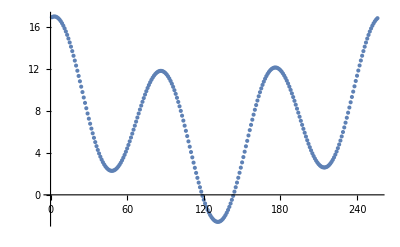

```mathematica
Δ=π/128;
{b0,b1,b2}={7.2,3.4,6.3};
PData=Table[ b0+b1 Cos[t]+b2 Cos[3t]+Sin[3t],{t, 0, 2π-Δ, Δ}];
Length[PData]
Chop[Fourier[PData,FourierParameters->{1,-1}]/Length[PData]]
ListPlot[PData]
```

#### The DFT and the FFT

The DFT recipe
	X_k=∑_(j=0)^(n-1) x_j ⅇ^(-(2π ⅈ)/nk j)
is a computationally involved object! To compute X_1 it looks as though I need to compute n complex exponentials, multiply them by the entries of x_j and add them all up.  Not counting the exponentials this is n flops. Since I need to do each component of the transform X_(0:n-1) the total this way is n^2 flops.

However, there is a very clever recursive algorithm that lets you split an even sized Fourier transform into two half sized Fourier Transforms.  The result is an incredibly fast “essentially” linear algorithm.  Fourier based algorithms are sometimes slightly faster if the size of a data set is a power of 2.

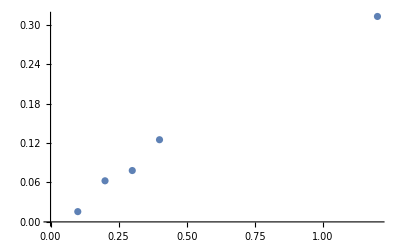

```mathematica
ns=10^6{1,2,3,4,12};
FTimes=Table[
x=RandomReal[{-1,1},n];
{n,Timing[Fourier[x];]⟦1⟧},
{n,ns}];
ListPlot[FTimes]
```

The inverse of the Fourier transform is essentially just another Fourier Transform.  There is almost always a command that uses the correct parameters to undo a Fourier transform.

```mathematica
x=RandomReal[{-1,1},10^6];
x-InverseFourier[Fourier[x]]
```

{0.+2.61416×10^-16 ⅈ,999998,1.66533×10^-16-2.0626×10^-16 ⅈ}
 |  |  |  |

Be careful, Mathematicians use parameters that make the inverse exactly equal to the transform. Electrical engineers and Physicists do not!  Mathematica uses the Physics convention by default!

## 2D: Pictures

#### 2D DFT

A 2D Fourier Transform just does the  transform on the rows and the columns.  The result is a way to count wiggles in two directions

```mathematica
f[x_,y_]:= 1+Cos[x]Sin[2y] +6Cos[3y]
Δ=2π/256;
Data=Table[ f[x,y],{x,0.0,2 π-Δ,Δ},{y,0.0, 2π-Δ,Δ}]ᵀ;
cp=6;
TabView[{
"3D-f"->Plot3D[ f[x,y],{x,0, 2π},{y,0,2π}],
"Contours-f"->ContourPlot[ f[x,y],{x,0, 2π},{y,0,2π}],
"Density-f"->DensityPlot[ f[x,y],{x,0, 2π},{y,0,2π}],
"Density"->ListDensityPlot[ Data],
"Fourier-Close Up"->MatrixForm[Chop[Fourier[Data]]⟦1;;cp,1;;cp⟧,TableHeadings->{Range[0,cp-1],Range[0,cp-1]}]
}]
```

12345

The 2D FFT algorithm is also essentially linear in the number of entries in the array.  In other words it is Fast!

#### FFT on images

A 2D FFT splits an image up into a sum of simpler images.  In real images things are pretty smooth so you can throw away a lot of the more rapidly wiggling components. This is what a JPEG compression does.

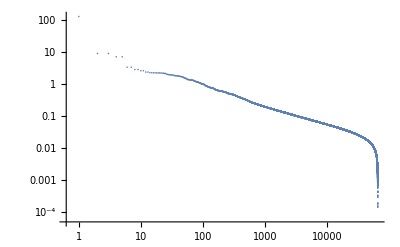

```mathematica
TestData=ImageData[ExampleData[{"TestImage","Moon"}]];
Dimensions[TestData];
FData=Fourier[TestData];
Hmm=Reverse[Sort[Flatten[Abs[FData]]]];
ListLogLogPlot[Hmm,
PlotRange->All,
GridLines->Automatic]
```

```mathematica
CompressedPic=Chop[InverseFourier[FData],0.3];
TabView[{
"Original"->Image[TestData],
"Compressed"->Image[CompressedPic],
"Original-Density"->ListDensityPlot[TestData,PlotLegends->Automatic],
"Compressed-Original"->ListDensityPlot[CompressedPic-TestData,PlotRange->All,PlotLegends->Automatic]
},2]
```

1234

```mathematica
?Histogram
```

```mathematica
f[x_,y_]:= 1+Cos[x]Sin[2y] +Sin[3y]
Δ=2π/256;
Data=Table[ f[x,y],{x,0.0,2 π-Δ,Δ},{y,0.0, 2π-Δ,Δ}]ᵀ;
cp=6;
TabView[{
"3D-f"->Plot3D[ f[x,y],{x,0, 2π},{y,0,2π}],
"Contours-f"->ContourPlot[ f[x,y],{x,0, 2π},{y,0,2π}],
"Density-f"->DensityPlot[ f[x,y],{x,0, 2π},{y,0,2π}],
"Density"->ListDensityPlot[ Data],
"Fourier-Close Up"->MatrixForm[Chop[Abs[Fourier[Data]]⟦1;;cp,1;;cp⟧],TableHeadings->{Range[0,cp-1],Range[0,cp-1]}]
}]
```

12345

The FFT algorithm is also essentially linear in the number of entries in the array.  In other words it is Fast!

### Rea